# SKS Initial conditions

## Import metric

```mathematica
Import["~/llgsks.mx"]
```

## Initial data elipse

```mathematica
ClearAll[elipseID];
elipseID[BHParams_,InitPos_,LocalEnergy_,ParticleMass_,param_]:=Module[
{llg,En,m,LEPUM,velNorm,AA,BB,CC,DD,FF,GG,Δ,J,II,α,β,X0,Y0,θ},

llg=llgSKS//.Ω->√((M1+M2)/b^3);
llg=llg//.{
M1->BHParams⟦1⟧,
M2->BHParams⟦2⟧,

a1->BHParams⟦3⟧,
a2->BHParams⟦4⟧,

b->BHParams⟦5⟧,

t->0,
x->InitPos⟦1⟧,
y->InitPos⟦2⟧,
z->0
};

En=LocalEnergy;
m=ParticleMass;

LEPUM=En/m;
velNorm=1-(1/LEPUM)^2;

AA=llg⟦2,2⟧;
BB=llg⟦2,3⟧;
CC=llg⟦3,3⟧;
DD=0;
FF=0;
GG=-velNorm;

Δ=Det[{{AA,BB,DD},{BB,CC,FF},{DD,FF,GG}}];
J=Det[{{AA,BB},{BB,CC}}];
II=AA+CC;

If[!(Δ≠0&&J>0&&Δ/II<0),
Print["Unphysical configuration"];
Abort[];
];

X0=(CC*DD-BB*FF)/(BB^2-AA*CC);
Y0=(AA*FF-BB*DD)/(BB^2-AA*CC);

α=√((2(AA*FF^2+CC*DD^2+GG*BB^2-2*BB*DD*FF-AA*CC*GG))/((BB^2-AA*CC)(√((AA-CC)^2+4*BB^2)-(AA+CC))));
β=√((2(AA*FF^2+CC*DD^2+GG*BB^2-2*BB*DD*FF-AA*CC*GG))/((BB^2-AA*CC)(-√((AA-CC)^2+4*BB^2)-(AA+CC))));

θ=Piecewise[
{
{0,BB==0&&AA<CC},
{π/2,BB==0&&AA>CC},
{ArcCot[(AA-CC)/(2BB)]/2,BB≠0&&AA<CC},
{π/2+ArcCot[(AA-CC)/(2BB)]/2,BB≠0&&AA>CC}
}
];

Return[{X0+α Cos[param] Cos[θ]-β Sin[param] Sin[θ],Y0+β Cos[θ] Sin[param]+α Cos[param] Sin[θ]}];
]
```

## Test

Vx = 0.6631090691914931
Vy = 0.6790724325845352

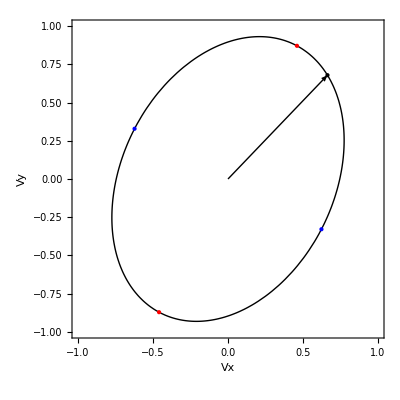

```mathematica
Block[
{M1,M2,a1,a2,b,x0,y0,z0,En,m,X0,Y0,α,β,θ,curve,pt},
M1=1/2;
M2=1/2;

a1=98/100M1;
a2=98/100M2;

b=10;

x0=63/10;
y0=0;

En=1;
m=1/100;

curve=elipseID[{M1,M2,a1,a2,b},{x0,y0},En,m,param];
pt=curve//.param->-25/200*π;

Print["Vx = ",N[pt⟦1⟧,16],"\nVy = ",N[pt⟦2⟧,16]];

ParametricPlot[
curve,
{param,0,2π},

PlotRange->{{-1,1},{-1,1}},
PlotStyle->Directive[Black,Thick],

Axes->False,
Frame->True,

FrameLabel->{"Vx","Vy"},

Epilog->{
PointSize[Large],
Red,
Point[curve//.param->0],
Point[curve//.param->π],

Blue,
Point[curve//.param->π/2],
Point[curve//.param->3π/2],

Black,
Arrow[{{0,0},pt}],
Point[pt]
}
]
]
```